# Adjacency Matrix Generation of Graphs

#### IGraph Installation and uploading

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: Paclet[IGraphM,0.3.108,<>].

It can now be loaded using the command Get["IGraphM`"].

```mathematica
<<IGraphM`
```

IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
IGLatticeMesh[]
```

{Square,Hexagonal,Triangular,Trihexagonal,SmallRhombitrihexagonal,TruncatedSquare,SnubSquare,TruncatedHexagonal,ElongatedTriangular,GreatRhombitrihexagonal,SnubHexagonal,Rhombille,DeltoidalTrihexagonal,TetrakisSquare,CairoPentagonal,TriakisTriangular,PrismaticPentagonal,BisectedHexagonal,FloretPentagonal,DellaRobbiaWeave,Portugal,StackBond,Herringbone,Basketweave,PersianHexagonalWeave,Hopscotch,StretcherBond,Pinwheel,BrickworkSquare,Chickenwire,Corridor,CorridorHorizontal,Brickweave,Trellis,HeeschIsohedral,PPentomino,Chevron,Shingle,Zigzag,Kite,FalseCubic,TrihexAndHex,GlideReflection,PentagonType1,PentagonType2,PentagonType3,PentagonType4,PentagonType5,PentagonType6,PentagonType7,PentagonType8,PentagonType9,PentagonType10,PentagonType11,PentagonType12,PentagonType13,PentagonType14,PentagonType15}

## Triangular Lattice

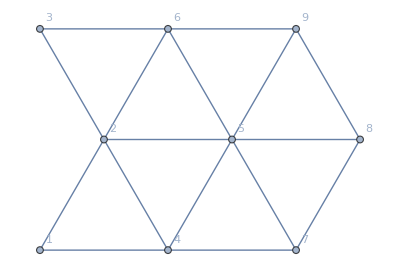

```mathematica
width =3;
height=width;
(* height=3;*)
graph=IGTriangularLattice[{height, width},VertexLabels->"Name"]
```

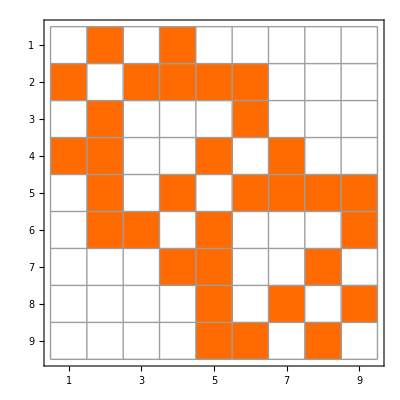

SparseArray[<32>, {9, 9}]

```mathematica
IGAdjacencyMatrixPlot[graph]
triangular$adjmat= AdjacencyMatrix[graph]
```

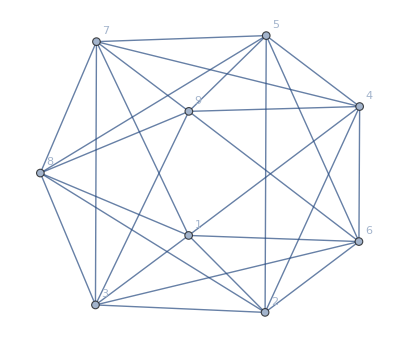

```mathematica
periodic$graph=IGTriangularLattice[{height, width}, "Periodic"-> True, VertexLabels->"Name"]
```

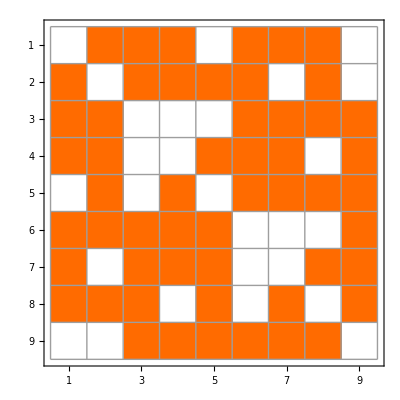

```mathematica
IGAdjacencyMatrixPlot[periodic$graph]
triangular$periodic$adjmat= Normal[AdjacencyMatrix[periodic$graph]];
```

#### This function can generate the next nearest neighbors from any adjacency matrix

```mathematica
nextneighborconnections=ConstantArray[0,{width*height,width*height}];
For[i=1, i≤ width*height, i++,
	c= triangular$periodic$adjmat[[i]]; (* Get a binary array of the connections to point i *)
	nnconn=c*triangular$periodic$adjmat; (* Get matrix with connections of the connections of i *)
	rm$i = ConstantArray[1,width*height]; 
	rm$i[[i]]=0; (* for deleting the nearest neighbor connections *)
	For[j=1, j≤width*height,j++,
	nnconn[[j]]=nnconn[[j]]*(-1*(c-1)); (* Gets rid of repeating connections those that go back to nearest neighbor points *)
	nnconn[[j]]=nnconn[[j]]*rm$i                           (* gets rid of nearest neighbor connections of i *) 
];
nextneighborconnections[[i]]=Total[nnconn]
 (* sums up the columns and defines that as the connections of point i *)
];
nextneighborconnections//MatrixForm
```

(0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 5
0 | 0 | 0 | 5 | 5 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0 | 0 | 5 | 0
5 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5 | 5 | 0
0 | 5 | 0 | 0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 5 | 0 | 5 | 0 | 0 | 0
5 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

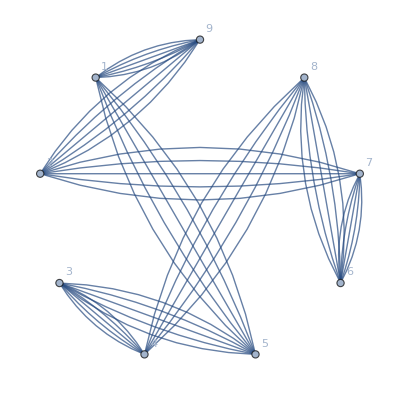

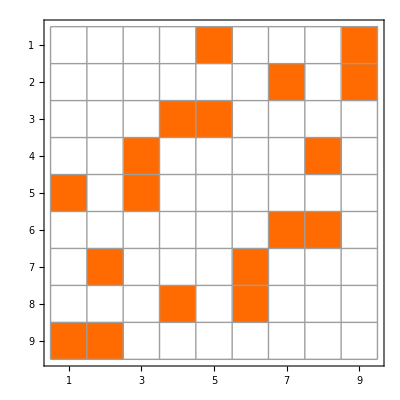

```mathematica
nn$graph=AdjacencyGraph[nextneighborconnections,VertexLabels->"Name"]
IGAdjacencyMatrixPlot[nn$graph]
```

```mathematica
Total[Total[triangular$periodic$adjmat*nextneighborconnections]] (* Just a sanity check should be 0 *)
```

0

```mathematica
triangular$periodic$adjmat.triangular$periodic$adjmat//MatrixForm
```

(6 | 4 | 4 | 3 | 5 | 3 | 3 | 3 | 5
4 | 6 | 3 | 3 | 3 | 4 | 5 | 3 | 5
4 | 3 | 6 | 5 | 5 | 3 | 3 | 4 | 3
3 | 3 | 5 | 6 | 4 | 4 | 3 | 5 | 3
5 | 3 | 5 | 4 | 6 | 3 | 3 | 3 | 4
3 | 4 | 3 | 4 | 3 | 6 | 5 | 5 | 3
3 | 5 | 3 | 3 | 3 | 5 | 6 | 4 | 4
3 | 3 | 4 | 5 | 3 | 5 | 4 | 6 | 3
5 | 5 | 3 | 3 | 4 | 3 | 4 | 3 | 6)

### Export the data

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
triangular$periodic$adjmat=SparseArray[triangular$periodic$adjmat];
nextneighborconnections= SparseArray[nextneighborconnections];
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangularperiodic_edges_"<>ToString[VertexCount[periodic$graph]]<>"_vertices.txt",triangular$periodic$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangular_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",triangular$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangularperiodicnextneighbor_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",nextneighborconnections,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangularperiodic_edges_9_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangular_edges_9_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/triangularperiodicnextneighbor_edges_9_vertices.txt

```mathematica
nextneighborconnections
```

SparseArray[<18>, {9, 9}]

## Square Lattice

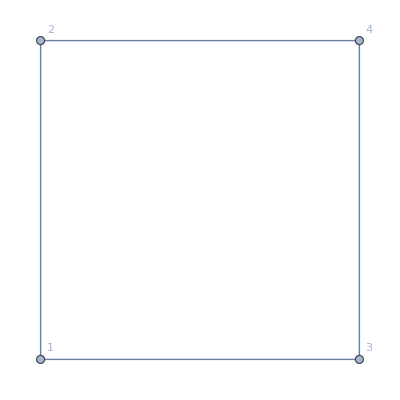

```mathematica
width =2; (*height=4;*)
height=width;
graph=IGSquareLattice[{height, width},VertexLabels->"Name" ]
```

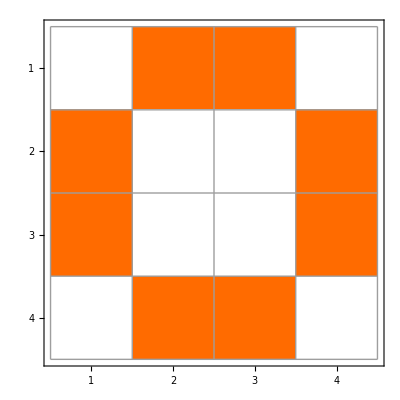

SparseArray[<8>, {4, 4}]

```mathematica
IGAdjacencyMatrixPlot[graph]
square$adjmat= AdjacencyMatrix[graph]
```

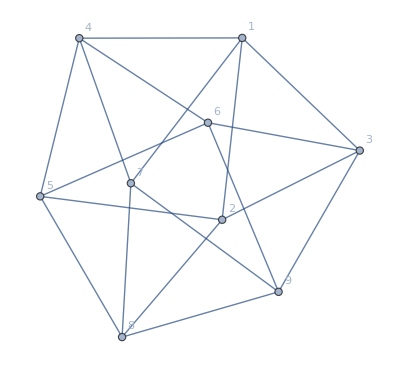

```mathematica
periodic$graph=IGSquareLattice[{height, width}, "Periodic"-> True,VertexLabels->"Name"]
```

```mathematica
IGAdjacencyMatrixPlot[periodic$graph]
square$periodic$adjmat= AdjacencyMatrix[periodic$graph]
```

-Graphics-

SparseArray[<8>, {4, 4}]

### Export the data

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/squareperiodic_edges_"<>ToString[VertexCount[periodic$graph]]<>"_vertices.txt",square$periodic$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/square_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",square$adjmat,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/squareperiodic_edges_4_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/square_edges_4_vertices.txt

## Hexagonal

```mathematica
width =3; (*height=4;*)
height=width;
{n,m} = {height,width};
graph=IGMeshGraph[IGLatticeMesh["Hexagonal",{n, m}], VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
VertexCount[graph]
```

-Graphics-

30

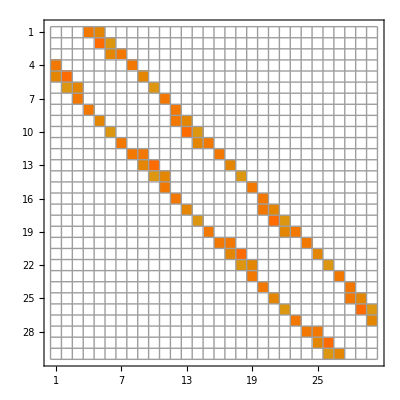

```mathematica
IGAdjacencyMatrixPlot[graph]
hex$adjmat= AdjacencyMatrix[graph];
```

{7→4,11→8,15→12,19→16,23→20,27→24}

{25→1,26→2,27→3,28→4,29→5,30→6}

{24→3}

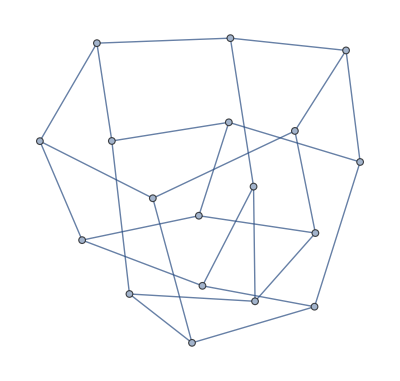

-Graphics-

```mathematica
bottom=Range[m+1,2 n (m+1),m+1];
repl1=Thread[bottom+m->bottom]
left=Range[1,2 m];
repl2=Thread[left+2 n (m+1)->left]
repl3={2 n (m+1)->m}
pgraph=SimpleGraph@Fold[VertexReplace,graph,{repl1,repl2,repl3}]

coord=AssociationThread[VertexList[graph],GraphEmbedding[graph]];
pgraph=Graph[pgraph,VertexCoordinates->Normal@KeyTake[coord,VertexList[pgraph]],VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
```

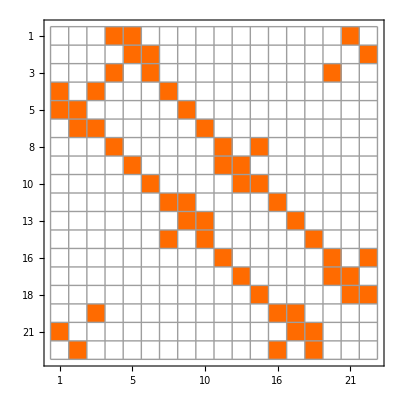

SparseArray[<54>, {18, 18}]

```mathematica
IGAdjacencyMatrixPlot[pgraph]
hex$periodic$adjmat= AdjacencyMatrix[pgraph]
```

### Export the data

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/hexagonalperiodic_edges_"<>ToString[VertexCount[pgraph]]<>"_vertices.txt",hex$periodic$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/hexagonal_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",hex$adjmat,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/hexagonalperiodic_edges_18_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/hexagonal_edges_30_vertices.txt

## Kagome / Trihexagonal

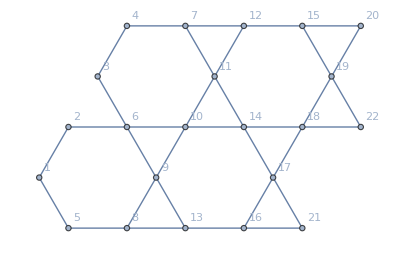

22

```mathematica
width =2; (*height=4;*)
height=width;
graph=IGMeshGraph[IGLatticeMesh["Trihexagonal",{height, width}], VertexLabels->"Name"]
size=VertexCount[graph]
```

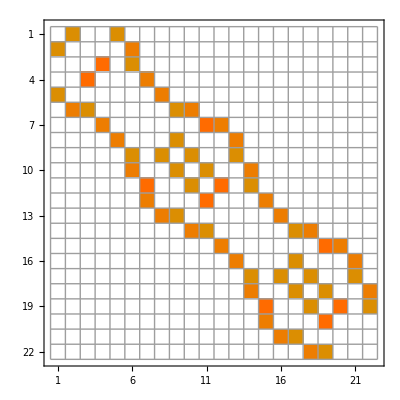

```mathematica
IGAdjacencyMatrixPlot[graph]
trihex$adjmat= AdjacencyMatrix[graph];
```

### Periodic Trihexagonal

#### Visualization of periodic BC

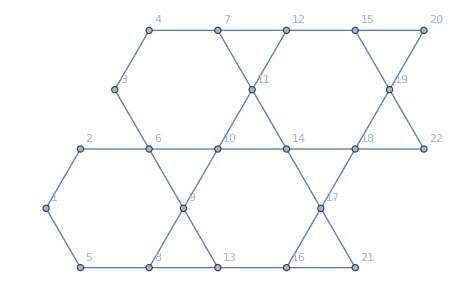

-Graphics-

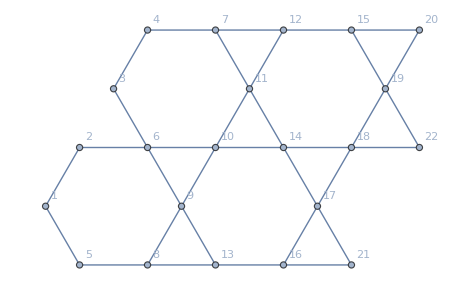
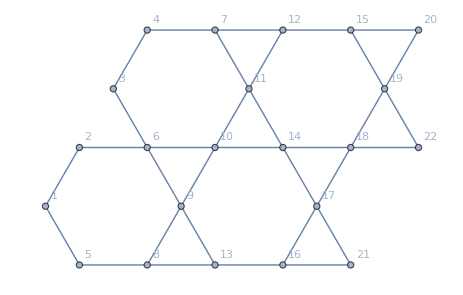
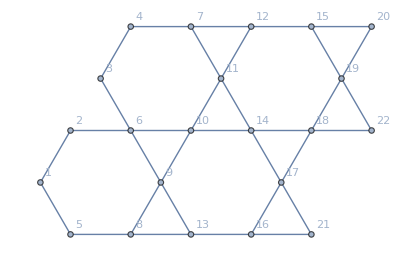

-Graphics- -Graphics-

-Graphics-

#### Matrix Recreation

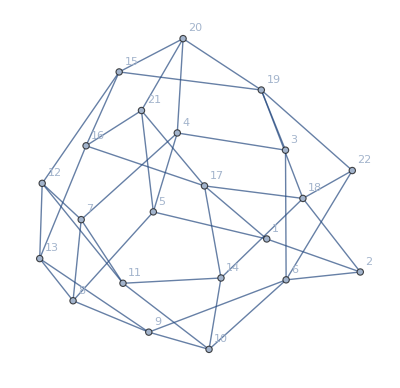

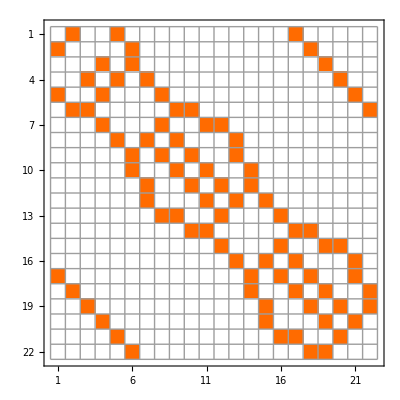

-Graphics-

```mathematica
periodic$trihex$adjmat=trihex$adjmat;
n=width;
(*For Left and Right connection*)
For[ii=1,ii≤ 3*n,ii++,
periodic$trihex$adjmat[[ii,ii+(VertexCount[graph]-3n)]]=1;
periodic$trihex$adjmat[[ii+(VertexCount[graph]-3n),ii]]=1;
]
(*For Top and Bottom connection*)
count=0;
jj=2n;
While[jj<VertexCount[graph],
periodic$trihex$adjmat[[jj,jj+1]]=1;
periodic$trihex$adjmat[[jj+1,jj]]=1;
If[Mod[count,2]==0,jj=jj+(n+1)];
If[Mod[count,2]==1,jj=jj+2n+1];
count=count+1;
]
periodic$trihex$graph=AdjacencyGraph[periodic$trihex$adjmat,VertexLabels->"Name" ]
IGAdjacencyMatrixPlot[periodic$trihex$graph]

coord=AssociationThread[VertexList[graph],GraphEmbedding[periodic$trihex$graph]];
periodic$trihex$graph=Graph[periodic$trihex$graph,VertexCoordinates->Normal@KeyTake[coord,VertexList[periodic$trihex$graph]],VertexShapeFunction->"Name",PerformanceGoal->"Quality"]
```

### Export the data

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/trihexagonal_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",trihex$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/trihexagonalperiodic_edges_"<>ToString[VertexCount[graph]]<>"_vertices.txt",periodic$trihex$adjmat,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/trihexagonal_edges_22_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/trihexagonalperiodic_edges_22_vertices.txt

## Checkerboard

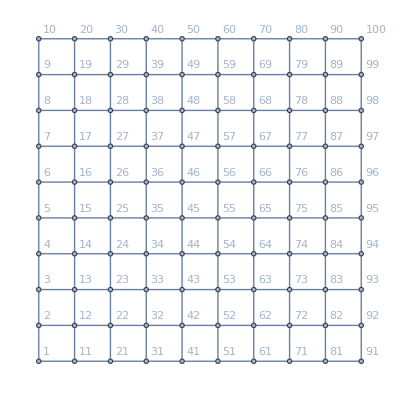

100

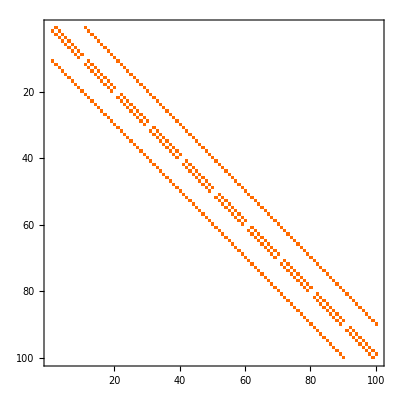

```mathematica
width =9; (*height=4;*)
n=width;
height=width;
(*graph=IGSquareLattice[{height+1, width+1},VertexLabels->"Name" ]*)
graph=IGMeshGraph[IGLatticeMesh["Square",{height, width}], VertexLabels->"Name"]
VertexCount[graph]
IGAdjacencyMatrixPlot[graph]
original$adjmat= AdjacencyMatrix[graph];
```

#### Periodic

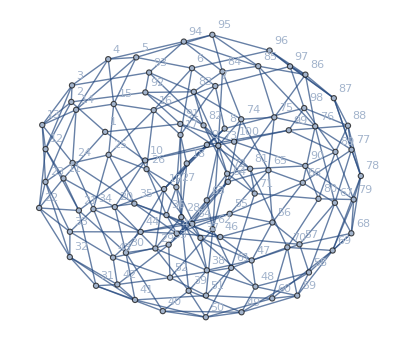

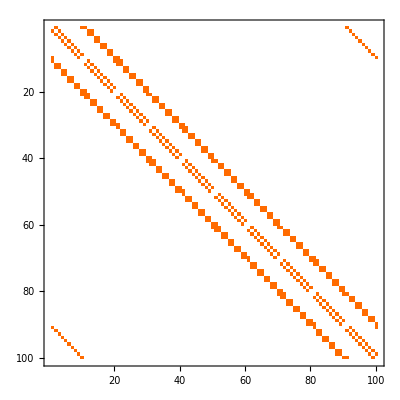

```mathematica
(*periodic$graph=IGSquareLattice[{height+1, width+1}, "Periodic"-> True,VertexLabels->"Name"]
periodic$adjmat= AdjacencyMatrix[periodic$graph];
checker$periodic$adjmat=periodic$adjmat;*)
checker$periodic$adjmat=original$adjmat;
count=0;
For[i=1, i<=(n+1)^2,i++,
count=count+1;
If[Mod[n,2]==1 && Mod[i,n+1]==1, count=count+1];
(*top left to bot right*)
If[ Mod[count,2]==0,
checker$periodic$adjmat[[i,i+n]]=1;
checker$periodic$adjmat[[i+n,i]]=1;]
If[Mod[count,2]==1,
(*bot left to top right*)
checker$periodic$adjmat[[i,i+(n+2)]]=1;
checker$periodic$adjmat[[i+(n+2),i]]=1;]
(*making periodic*)
If[Mod[i,n+1]==0, 
checker$periodic$adjmat[[i,i+1-(n+1)]]=1;
checker$periodic$adjmat[[i+1-(n+1),i]]=1;]
If[i≤(n+1), 
checker$periodic$adjmat[[i,i+VertexCount[graph]-(n+1)]]=1;
checker$periodic$adjmat[[i+VertexCount[graph]-(n+1),i]]=1; ]
] //Quiet
periodic$checker$graph=AdjacencyGraph[checker$periodic$adjmat,VertexLabels->"Name"]
IGAdjacencyMatrixPlot[periodic$checker$graph]
```

#### Non-Periodic

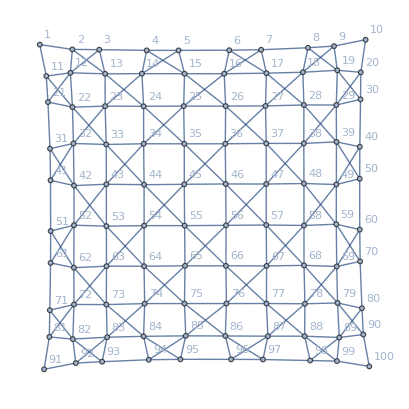

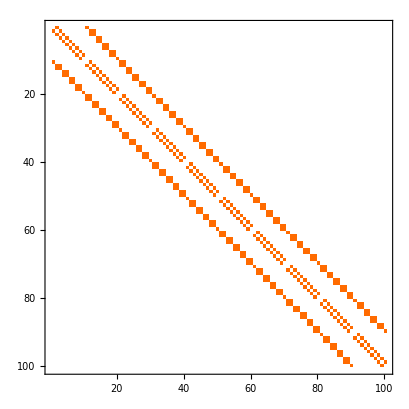

```mathematica
checker$adjmat=original$adjmat;
count=0;
For[i=1, i<(n+1)^2,i++,
count=count+1;
If[Mod[n,2]==1 && Mod[i,n+1]==1, count=count+1];
(*top left to bot right*)
If[Mod[i,(n+1)]≠1 && Mod[count,2]==0,
checker$adjmat[[i,i+n]]=1;
checker$adjmat[[i+n,i]]=1; ]
(*bot left to top right*)
If[Mod[i,(n+1)]≠0 && Mod[count,2]==1,
checker$adjmat[[i,i+(n+2)]]=1;
checker$adjmat[[i+(n+2),i]]=1; ]
] //Quiet
checker$graph=AdjacencyGraph[checker$adjmat, VertexLabels->"Name"]
IGAdjacencyMatrixPlot[checker$graph]
```

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/checkerperiodic_edges_"<>ToString[VertexCount[periodic$checker$graph]]<>"_vertices.txt",checker$periodic$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/checker_edges_"<>ToString[VertexCount[checker$graph]]<>"_vertices.txt",checker$adjmat,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/checkerperiodic_edges_100_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/checker_edges_100_vertices.txt

## Toric Square Latt Adjmat

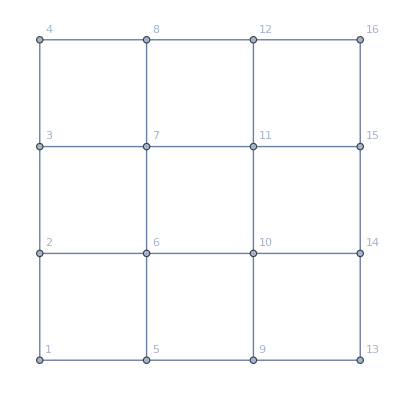

```mathematica
width =4; (*height=4;*)
height=width;
(*graph=IGSquareLattice[{height, width},VertexLabels->"Name" ]*)
graph=IGMeshGraph[IGLatticeMesh["Square",{height-1, width-1}], VertexLabels->"Name"]
```

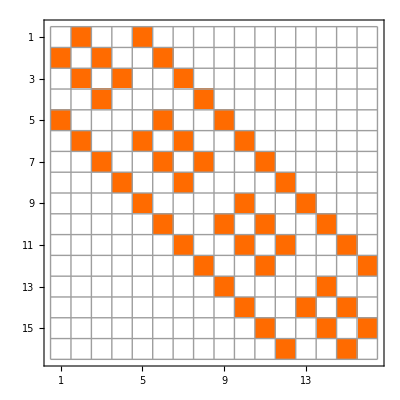

SparseArray[<48>, {16, 16}]

```mathematica
IGAdjacencyMatrixPlot[graph]
square$adjmat= AdjacencyMatrix[graph]
```

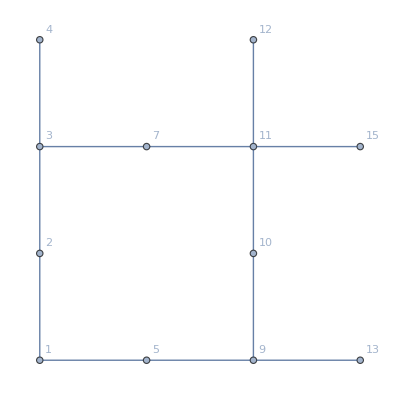

```mathematica
graph=VertexDelete[graph,{6,8,14,16}]
```

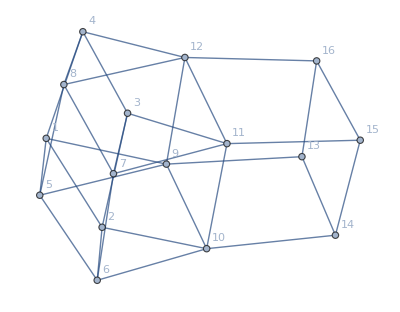

IGAdjacencyMatrixPlot[SparseArray[<64>, {16, 16}]]

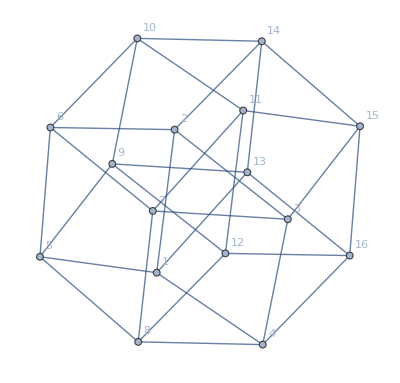

```mathematica
periodic$square$adjmat=square$adjmat;
n=width;
For[i=1, i<=(n+1)^2,i++,
(*making periodic*)
If[Mod[i,n]==0, 
periodic$square$adjmat[[i,i+1-n]]=1;
periodic$square$adjmat[[i+1-n,i]]=1;]
If[i≤n, 
periodic$square$adjmat[[i,i+VertexCount[graph]-n]]=1;
periodic$square$adjmat[[i+VertexCount[graph]-n,i]]=1; ]
] //Quiet
periodic$square$graph=AdjacencyGraph[periodic$square$adjmat,VertexLabels->"Name"]
IGAdjacencyMatrixPlot[periodic$square$adjmat]
periodic$square$graph=IGSquareLattice[{height, width}, "Periodic"-> True,VertexLabels->"Name"]
```

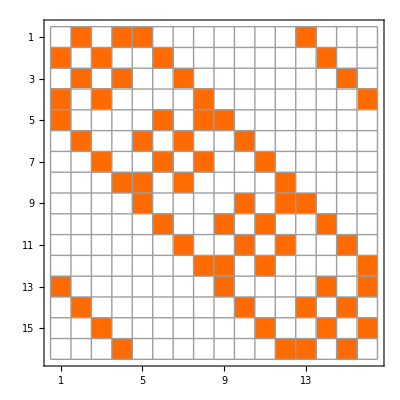

SparseArray[<64>, {16, 16}]

```mathematica
IGAdjacencyMatrixPlot[periodic$square$graph]
square$periodic$adjmat= AdjacencyMatrix[periodic$square$graph]
```

-Graphics-

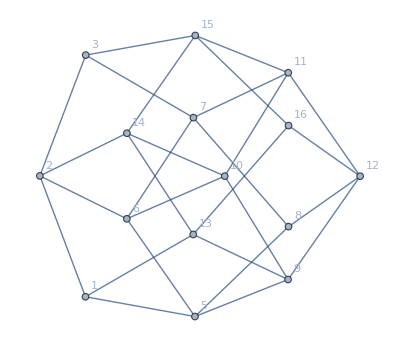

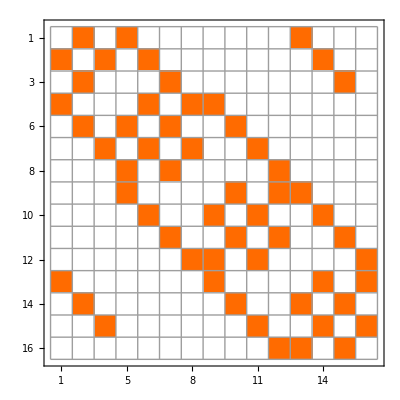

SparseArray[<56>, {15, 15}]

```mathematica
graph=AdjacencyGraph[square$periodic$adjmat,VertexLabels->"Name"]
graph=VertexDelete[graph,{4}]
IGAdjacencyMatrixPlot[graph]
int1$adjmat= AdjacencyMatrix[graph]
```

-Graphics-

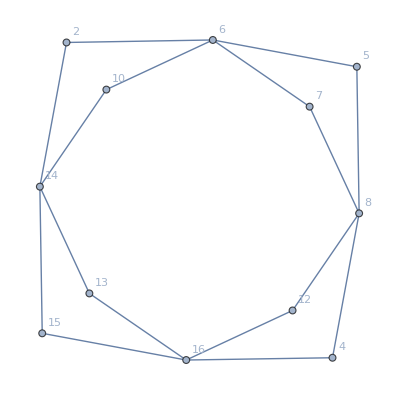

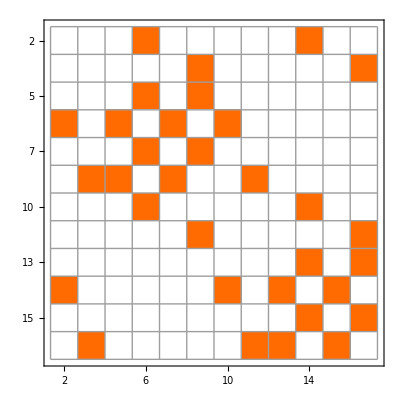

SparseArray[<32>, {12, 12}]

```mathematica
graph=AdjacencyGraph[square$periodic$adjmat,VertexLabels->"Name"]
graph=VertexDelete[graph,{1,3,9,11}]
IGAdjacencyMatrixPlot[graph]
int2$adjmat= AdjacencyMatrix[graph]
```

### Export the data

#### Exporting the adjacency list as a sparse matrix to numpy:

```mathematica
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/toric_int1_edges_"<>ToString[width^2]<>"_vertices.txt",int1$adjmat,"MTX"]
Export["C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/toric_int2_edges_"<>ToString[width^2]<>"_vertices.txt",int2$adjmat,"MTX"]
```

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/toric_int1_edges_16_vertices.txt

C://Users/HP/Documents/Quantum_Machine_Learning_Research/NetKet/netket-1.0.5/Tutorials/Ising2d/Edgemats/toric_int2_edges_16_vertices.txt

## Other Int

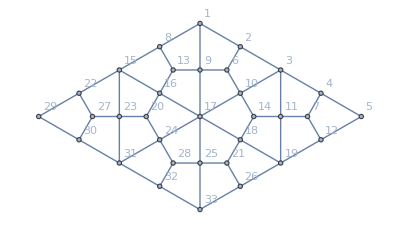

```mathematica
width =2; (*height=4;*)
height=width;
graph=IGMeshGraph[IGLatticeMesh["DeltoidalTrihexagonal",{height, width}], VertexLabels->"Name"]
```

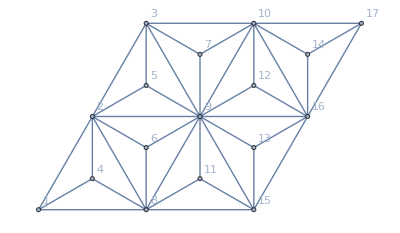

```mathematica
width =2; (*height=4;*)
height=width;
graph=IGMeshGraph[IGLatticeMesh["TriakisTriangular",{height, width}], VertexLabels->"Name"]
```

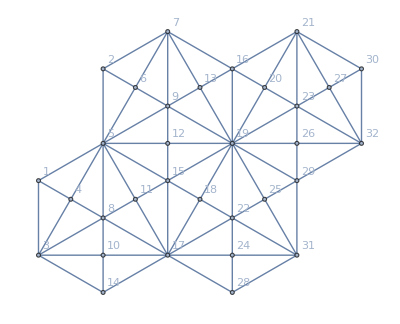

```mathematica
width =2; (*height=4;*)
height=width;
graph=IGMeshGraph[IGLatticeMesh["BisectedHexagonal",{height, width}], VertexLabels->"Name"]
```